```mathematica
data=Import[FileNameJoin[{NotebookDirectory[],"clipped-captures-bloc-calibration","center-finder_centroid_log.csv"}],"Table","FieldSeparators"->";"];
X=data[[All,3]][[1;;12000]];
Y=data[[All,4]][[1;;12000]];
XY=data[[All,{3,4}]][[1;;12000]];
```

```mathematica
BoxWhiskerChartCenterFinder[Y_]:=BoxWhiskerChart[Partition[Y,150],"Outliers",Joined->True]
DistributionChartCenterFinder[Y_]:=DistributionChart[Partition[Y,150]]
```

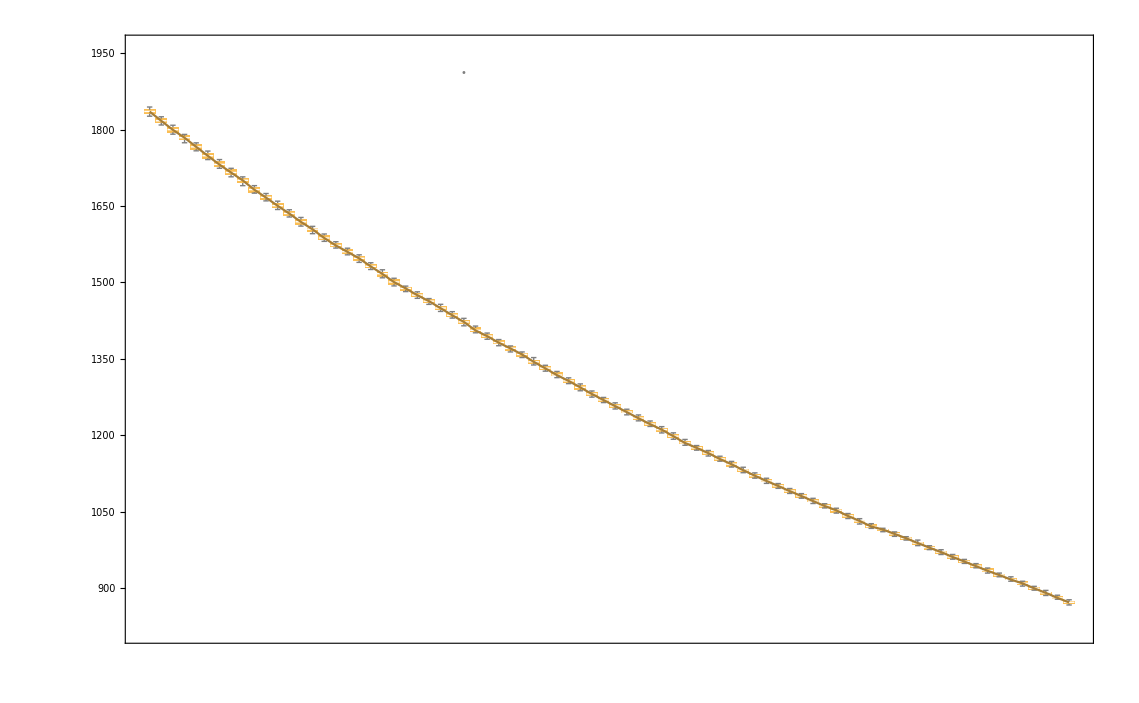

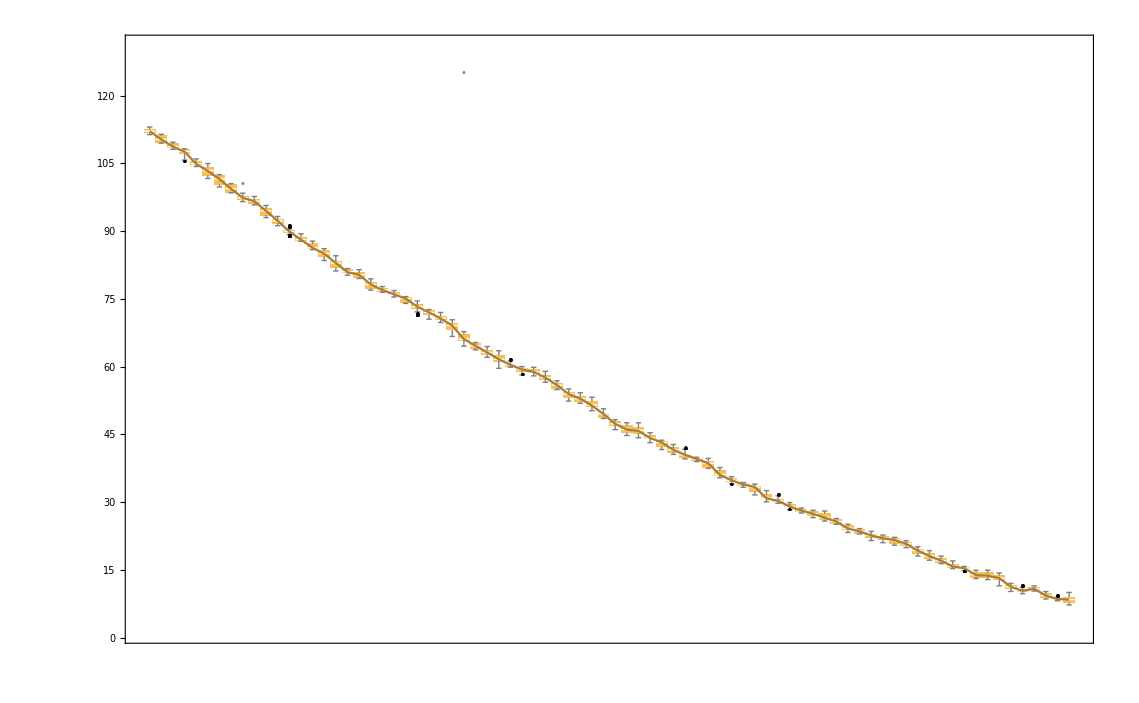

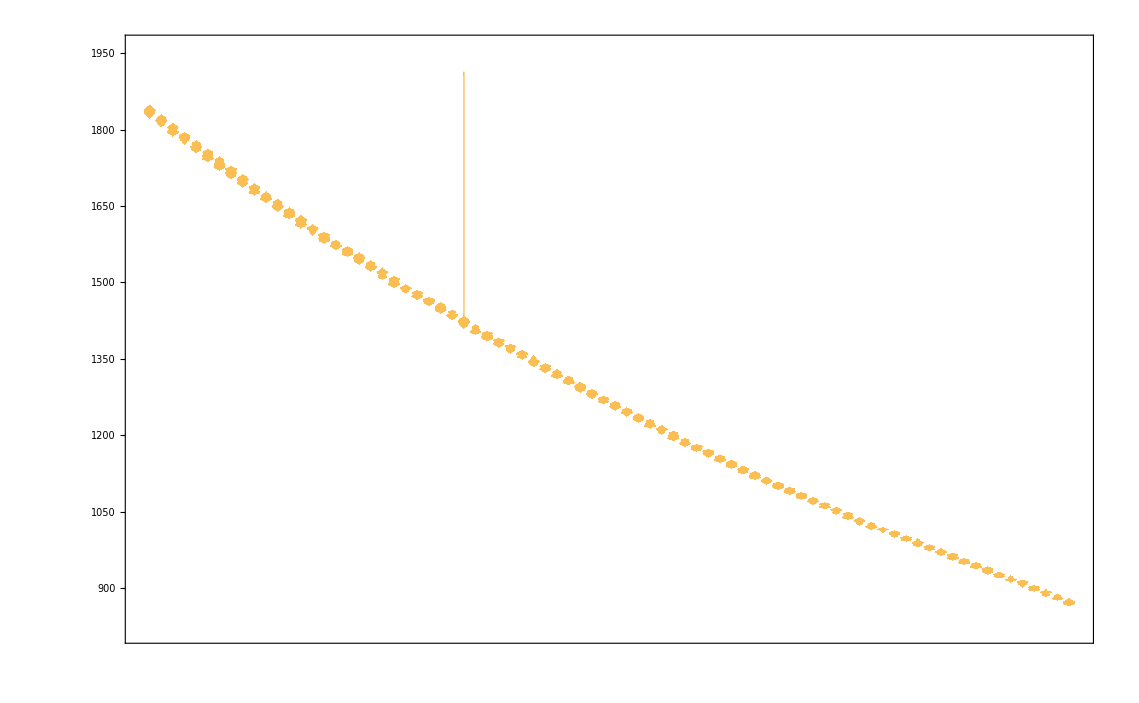

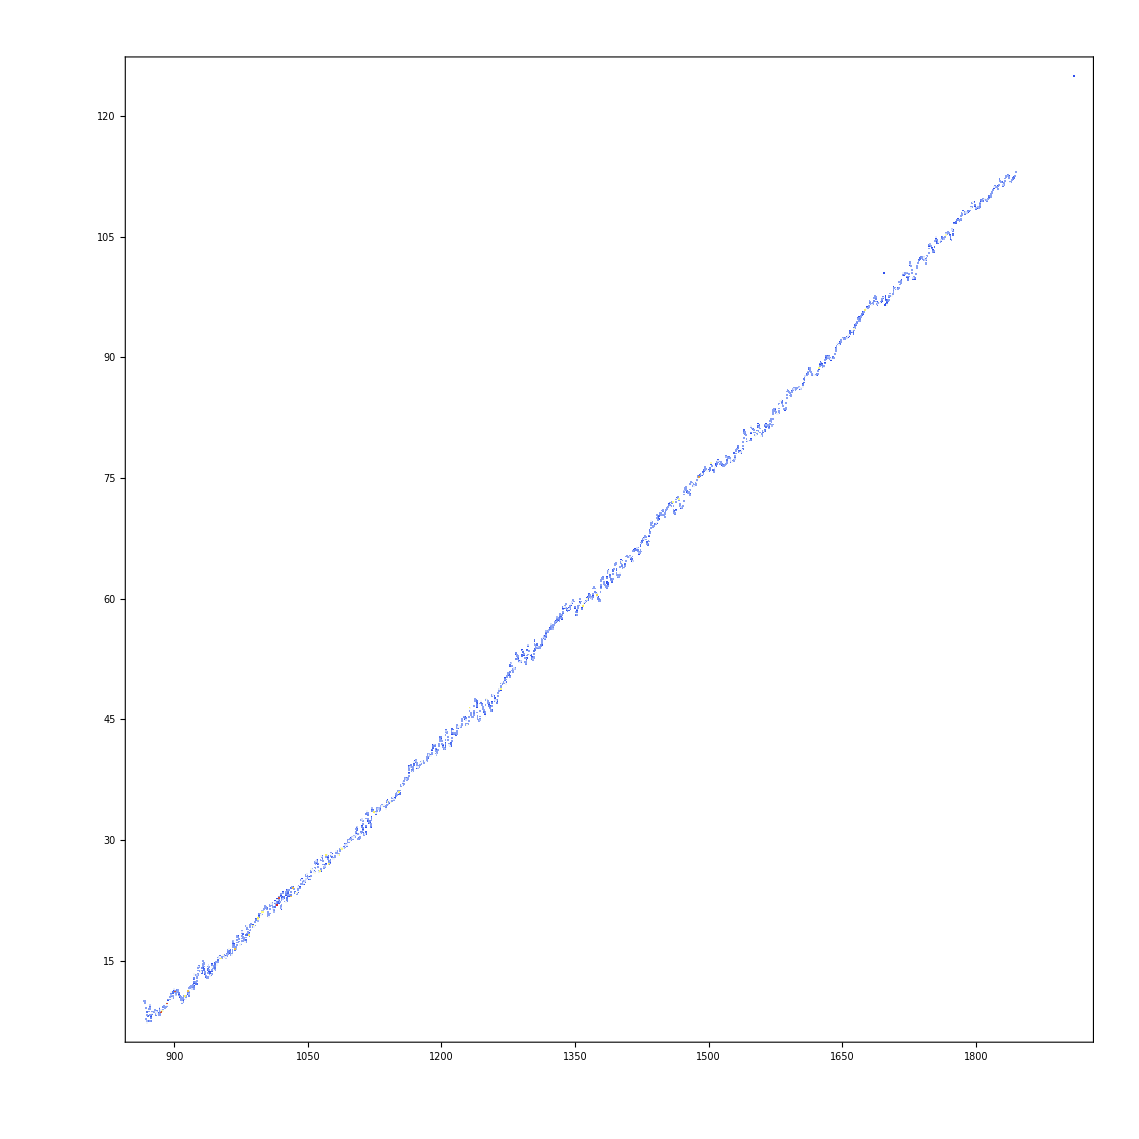

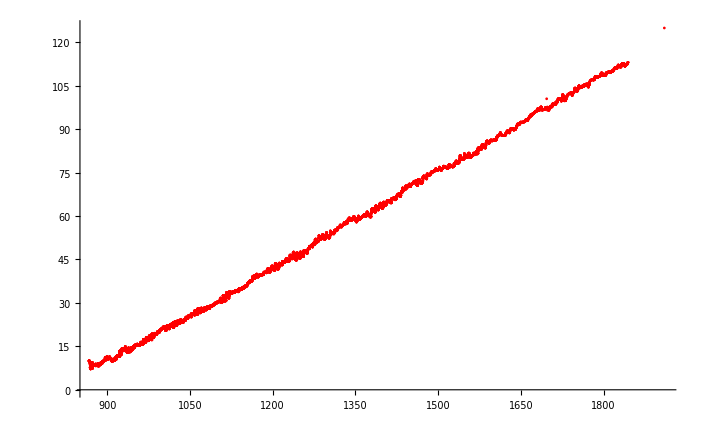

```mathematica
BoxWhiskerChartCenterFinder[X]
BoxWhiskerChartCenterFinder[Y]
DistributionChartCenterFinder[X]
DensityHistogram[XY,1000,ColorFunction->"TemperatureMap"]
Show[ListPlot[XY,PlotStyle->Red],ContourPlot[PDF[xydist,{x,y}],{x,0,2 π},{y,-1.4,1.4},PlotRange->All,Contours->{0.02301837725113296,0.09301835502825319,0.1641455150120073,0.27931426505406887},ContourStyle->Gray,ContourShading->None],ImageSize->Large]
```